```mathematica
f[x_] = x BesselJ[0,x] Exp[x-x^2/(4 2^2)];
```

```mathematica
f1[x_] = 1/(1!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,1}];
f2[x_] = 1/(2!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,2}];
f3[x_] = 1/(3!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,3}];
f4[x_] = 1/(4!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,4}];
f5[x_] = 1/(5!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,5}];
f6[x_] = 1/(6!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,6}];
f7[x_] = 1/(7!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,7}];
f8[x_] = 1/(8!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,8}];
f9[x_] = 1/(9!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,9}];
f10[x_] = 1/(10!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,10}];
f11[x_] = 1/(11!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,11}];
f12[x_] = 1/(12!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,12}];
f13[x_] = 1/(13!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,13}];
f14[x_] = 1/(14!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,14}];
f15[x_] = 1/(15!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,15}];
f16[x_] = 1/(16!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,16}];
f17[x_] = 1/(17!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,17}];
f18[x_] = 1/(18!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,18}];
f19[x_] = 1/(19!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,19}];
f20[x_] = 1/(20!)D[x BesselJ[0,x] Exp[-x^2/(4 2^2)],{x,20}];
```

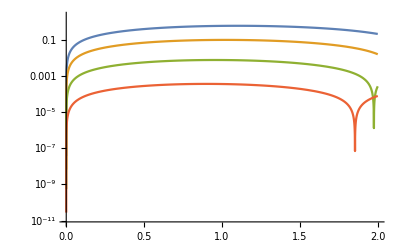

```mathematica
LogPlot[{Abs[f2[x]],Abs[f4[x]],Abs[-f6[x]],Abs[f8[x]]},{x,0,2},PlotRange->All]
```

```mathematica
Abs[f4[1/2 BesselJZero[0,1]]//N]
```

0.103033

```mathematica
BesselJZero[0,1]/2//N
```

1.20241

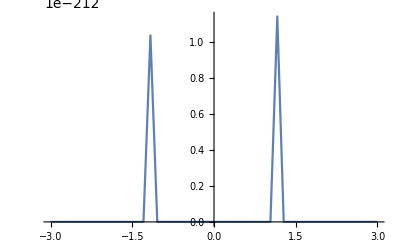

```mathematica
Plot[Exp[-Abs[Im[((2π)/h π(x+I y)Tanh[π/2 Sinh[(x+I y)]])]]/.y-> π/3/.h-> 0.01], {x,-3,3}, PlotRange->All]
```

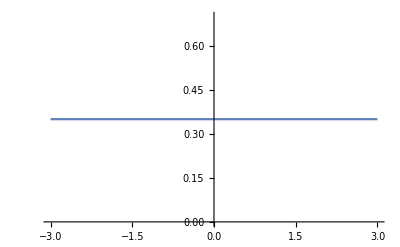

```mathematica
Plot[Exp[-Abs[Im[((2π)/h(x+I y)Tanh[π/2 Sinh[(x+I y)]])]]/.y-> π/3/.h-> 0.01], {x,-3,3}, PlotRange->All]
```

```mathematica
-Integrate[(x^2+y^2)^(1/4)Exp[-Abs[x]/λ], {x, Infinity,-Infinity}, Assumptions->{y>0,λ>0}]+Integrate[(x^2+y^2)^(1/4)Exp[-Abs[x]/λ], {x, -Infinity,Infinity}, Assumptions->{y>0,λ>0}]
```

(4 2^(1/4) π^(3/2) (y λ)^(3/4) (BesselY[3/4,y/λ]-StruveH[3/4,y/λ]))/Gamma[-1/4]

```mathematica
u[x_,y_] = Simplify[Re[ComplexExpand[Exp[-(x+I y)^2]]], Assumptions->{x>0,y>0}]
v[x_, y_] = Simplify[Im[ComplexExpand[Exp[-(x+I y)^2]]], Assumptions->{x>0,y>0}]
```

ⅇ^(-x^2+y^2) Cos[2 x y]

-ⅇ^(-x^2+y^2) Sin[2 x y]

```mathematica
D[u[x,y],y]+D[v[x,y],x]
```

0

```mathematica
Simplify[u[x,y]^2+v[x,y]^2]
```

ⅇ^(-2 x^2+2 y^2)

```mathematica
Plot3D[Abs[Exp[-(x+I y)]],{x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
π/h((x+I y)Tanh[π/2 Sinh[x+I y]])/.x-> 20/.y-> π/3//N
((x+I y)Tanh[π/2 Sinh[x+I y]])/.x-> 20/.y->- π/3//N
```

(62.8319+3.28987 ⅈ)/h

20.-1.0472 ⅈ

```mathematica
(π/h(x+I y)Tanh[π/2 Sinh[x+I y]])/.x-> 0
```

-(π y Tan[1/2 π Sin[y]])/h

```mathematica
((x+I y)Tanh[π/2 Sinh[x+I y]])/.y->- π/3/.x-> 20//N
```

20.-1.0472 ⅈ

```mathematica
((x+I y)Tanh[π/2 Sinh[x+I y]])/.y-> π/3/.x-> 20//N
```

20.+1.0472 ⅈ

```mathematica
Simplify[Re[ComplexExpand[((x+I y)Tanh[π/2 Sinh[x+I y]])/.x-> 0]],Assumptions->{Element[{y,Cos[π Sin[y]]},Reals]}]
Simplify[Im[ComplexExpand[((x+I y)Tanh[π/2 Sinh[x+I y]])/.x-> 0]],Assumptions->{Element[{y,Cos[π Sin[y]]},Reals]}]
```

-y Re[1/(1+Cos[π Sin[y]])] Sin[π Sin[y]]

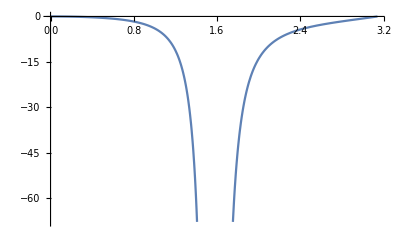

```mathematica
Plot[-y Re[1/(1+Cos[π Sin[y]])] Sin[π Sin[y]],{y,0,π}]
```

```mathematica
(100 π)/3//N
```

104.72

```mathematica
Integrate[(x^2+y^2)^(1/4)Exp[-x/λ], {x,R,-Imu}, Assumptions->{λ>0,R>0,Imu>0}]
```

Integrate[ⅇ^(-x/λ) (x^2+y^2)^(1/4),{x,R,-Imu},Assumptions→{λ>0,R>0,Imu>0}]

```mathematica
Integrate[(x^2+y^2)^(1/4)Exp[-x^2/(4 σ^2)], {x,Infinity,0}, Assumptions->{σ>0,y>0,α>0}]
```

-√(2 π) σ^(3/2) HypergeometricU[-1/4,1/4,y^2/(4 σ^2)]

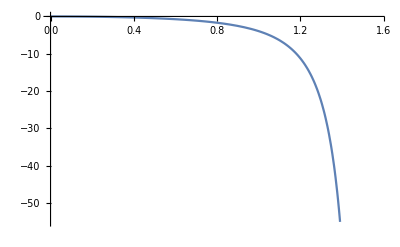

```mathematica
Plot[-y Tan[1/2 π Sin[y]], {y, 0,π/2}]
```

```mathematica
-y Tan[1/2 π Sin[y]]/.y-> π/2
```

ComplexInfinity

```mathematica
((x+I y)Tanh[π/2 Sinh[x+I y]])/.x-> 0
```

-y Tan[1/2 π Sin[y]]

```mathematica
Integrate[Exp[-1/(4 σ^2)(x+I y)^2], {x, -Infinity, Infinity}, Assumptions->{y>0,σ>0}]
```

2 √π σ

```mathematica
(Simplify[Re[ComplexExpand[(x+I y)Exp[-1/(4 σ^2)(x+I y)^2]]], Assumptions->{σ>0,Element[{x,y},Reals]}])^2
```

ⅇ^((-x^2+y^2)/(2 σ^2)) (x Cos[(x y)/(2 σ^2)]+y Sin[(x y)/(2 σ^2)])^2

```mathematica
(Simplify[Im[ComplexExpand[(x+I y)Exp[-1/(4 σ^2)(x+I y)^2]]], Assumptions->{σ>0,Element[{x,y},Reals]}])^2
```

ⅇ^((-x^2+y^2)/(2 σ^2)) (y Cos[(x y)/(2 σ^2)]-x Sin[(x y)/(2 σ^2)])^2

```mathematica
Sqrt[(%85+%86)//Expand//Simplify]
```

√(ⅇ^((-x^2+y^2)/(2 σ^2)) (x^2+y^2))

```mathematica
Integrate[(x^2+4 σ^4)^(1/4)Exp[-x^2/(4 σ^2)], {x, -Infinity, Infinity}, Assumptions->{σ>0}]
```

2 √(2 π) σ^(3/2) HypergeometricU[-1/4,1/4,σ^2]

```mathematica
Plot3D[%92Exp[-σ^2]*h*1/(2 π)^(3/2), {σ,0,3}, {h, 0.001,1}]
```

```mathematica
Simplify[Abs[Integrate[Sqrt[r]Exp[-1/(4 σ^2)r^2+I r], {r, -Infinity,Infinity}, Assumptions->{σ>0}]], Assumptions->{σ>0}]
```

√2 ⅇ^(-σ^2/2) σ^3 (BesselK[1/4,σ^2/2]+BesselK[3/4,σ^2/2])

```mathematica
TeXForm[%122]
```

\sqrt{2} e^{-\frac{\sigma ^2}{2}} \sigma ^3 \left(K_{\frac{1}{4}}\left(\frac{\sigma
   ^2}{2}\right)+K_{\frac{3}{4}}\left(\frac{\sigma ^2}{2}\right)\right)

```mathematica
error = Simplify[Abs[Integrate[Sqrt[r]Exp[-1/(4 σ^2)r^2+I r], {r, -Infinity,Infinity}, Assumptions->{σ>0}]], Assumptions->{σ>0}]
Plot3D[error*(2 h)/(2 π)^(3/2)/.h-> ArcSinh[(2 ArcTanh[(5 σ)/(n π)])/π]/n, {σ,0,10}, {n,10,100}]
```

√2 ⅇ^(-σ^2/2) σ^3 (BesselK[1/4,σ^2/2]+BesselK[3/4,σ^2/2])

-Graphics3D-

(ⅇ^(-σ^2/2) σ^3 ArcSinh[(2 ArcTanh[(5 σ)/(n π)])/π] (BesselK[1/4,σ^2/2]+BesselK[3/4,σ^2/2]))/(n π^(3/2))

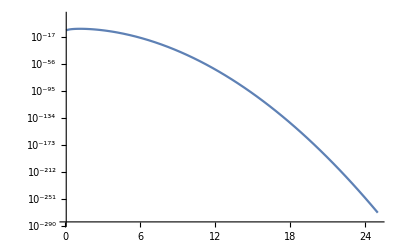

```mathematica
error = Simplify[Abs[Integrate[Sqrt[r]Exp[-1/(4 σ^2)r^2+I r], {r, -Infinity,Infinity}, Assumptions->{σ>0}]], Assumptions->{σ>0}]*(2 h)/(2 π)^(3/2)/.h-> ArcSinh[(2 ArcTanh[(5 σ)/(n π)])/π]/n
LogPlot[error/.n-> 100,{σ,0.1,25}]
```

```mathematica
Solve[x == π n Tanh[π/2 Sinh[h n]], h]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{h→ArcSinh[(2 ArcTanh[x/(n π)])/π]/n}}

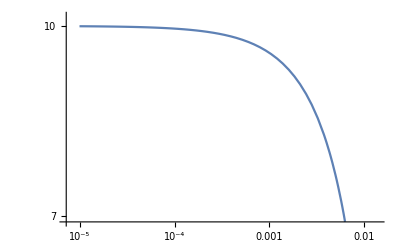

```mathematica
LogLogPlot[10 -π 10Tanh[π/2 Sinh[h 10]] ,{h,0.00001,0.01 }]
```

```mathematica
Integrate[Sqrt[x]Exp[-x^2/(4 σ^2)+I x], {x, -Infinity,Infinity}, {σ>0}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {σ>0}.

Integrate[ⅇ^(ⅈ x-x^2/(4 σ^2)) √x,{x,-∞,∞},{σ>0}]

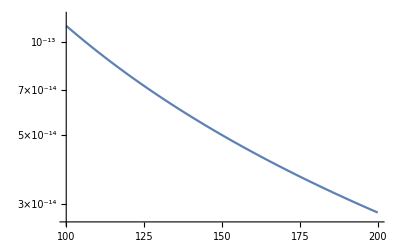

```mathematica
LogPlot[(%64*(2 h)/(2 π)^(3/2)/.h-> ArcSinh[(2 ArcTanh[(5 σ)/(n π)])/π]/n)/.σ-> 5, {n,100,200}, PlotRange->All]
```

```mathematica
Plot3D[ArcSinh[(2 ArcTanh[(5 σ)/(n π)])/π]/n, {σ, 0, 5},{n,5,10}, PlotRange->All]
```

-Graphics3D-

```mathematica
FindMaximum[f4[x],{x,1}]
```

FindMaximum::nrnum: The function value -Abs[0.159504 ⅇ^(-0.25/σ^2)+«11»+1.87409 (ⅇ^(-0.25 Power[«2»])-(0.5 ⅇ^Times[«2»])/σ^2)]/40320 is not a real number at {x} = {1.}.

FindMaximum[f4[x],{x,1}]

```mathematica
Simplify[Reduce[x == π n Tanh[π/2 Sinh[h n]], h], Assumptions->{n>0,x>0, x^2 ≠ n^2 π^2}]
```

(C[1]|C[2])∈Integers&&(h==(ⅈ (π+ArcSin[(2 ⅈ ArcTanh[x/(n π)]-2 π C[1])/π]+2 π C[2]))/n||h==(ⅈ (ArcSin[(2 (-ⅈ ArcTanh[x/(n π)]+π C[1]))/π]+2 π C[2]))/n)